```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6a *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[10^(4+((j-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((j-1)/5))/popsize genotypeabundances][[2]][[1]];
simv[[j]]={(4+((j-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(4+((j-1)/5)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryvext=Table[{(4+(j/25)),10^5 getTransV[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

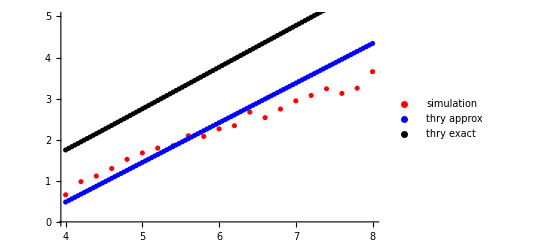

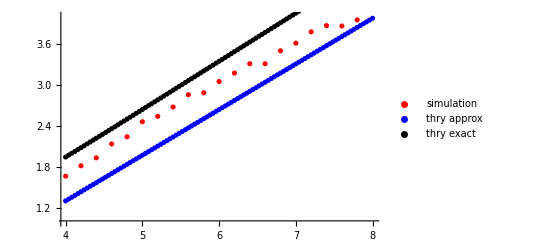

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp006.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,5}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,4}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((j-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simv[[j]]={(-4-((j-1)/10)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(-4-((j-1)/10)),Mean[results[[;;,9]]]/Δc1};
,{j,1,21}];
thryvest=Table[{(-4-(i/50)),(10^5 Δc1^2(2 Log[popsize Δc1]-Log[Δc1/10^(-4-(i/50))]))/(Log[Δc1/10^(-4-(i/50))]^2)},{i,0,100}];
thryvext=Table[{(-4-(i/50)),10^5 getTransV[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

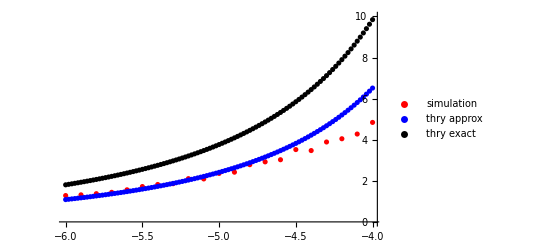

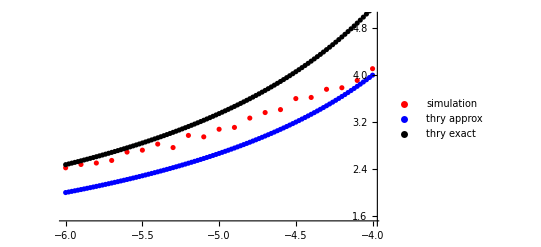

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp007.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,10}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1.5,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,21}];
simq=Table[{},{i,1,21}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

```mathematica
(* Run simulation *)
Do[
results=RunSimulationCheckEachMutation2[popsize,10^(-13/4+(j-1)/10),Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
simv[[j]]={(-13/4+(j-1)/10),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]};
simq[[j]]={(-13/4+(j-1)/10),Mean[results[[;;,9]]]/10^(-13/4+(j-1)/10)};
,{j,1,21}];
thryvest=Table[{(-13/4+(i/50)),(10^5 10^(2(-13/4+i/50))(2 Log[popsize 10^(-13/4+i/50)]-Log[10^(-13/4+i/50)/U1]))/(Log[10^(-13/4+i/50)/U1]^2)},{i,0,100}];
thryvext=Table[{(-13/4+(i/50)),10^5 getTransV[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
thryqest=Table[{(-13/4+(i/50)),(2 Log[popsize 10^(-13/4+i/50)])/Log[10^(-13/4+i/50)/U1]},{i,0,100}];
thryqext=Table[{(-13/4+(i/50)),getTransQ[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp008.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

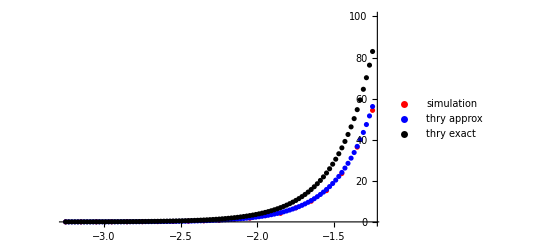

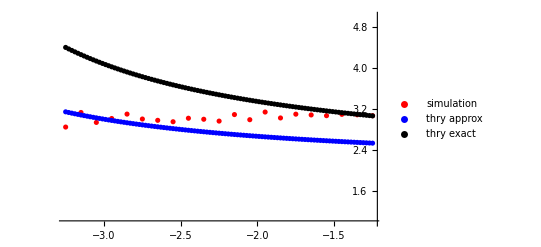

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp008.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,100}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.001,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={1,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,False};
(* Set initial genotypes and their abundances *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,False];
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
SeedRandom[7];
```

Trait 1 q = 3. in Concurrent Mutations Regime with expected time scale 2302.59 and rate of adaptation 4.34294×10^-7

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 a Examine Statistical Spread*)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata =ParallelTable[
results=RunSimulationCheckEachMutation2[10^(4+((Mod[j,21,1]-1)/5)),Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,10^(4+((Mod[j,21,1]-1)/5))/popsize genotypeabundances][[2]][[1]];
{{(4+((Mod[j,21,1]-1)/5)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(4+((Mod[j,21,1]-1)/5)),Mean[results[[;;,9]]]/Δc1}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m"];
thryvest=Table[{(4+(j/25)),(10^5 Δc1^2(2 Log[Δc1 10^(4+(j/25))]-Log[Δc1/U1]))/Log[Δc1/U1]^2},{j,0,100}];
thryvext=Table[{(4+(j/25)),10^5 getTransV[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
thryqest=Table[{(4+(j/25)),2((4+((j-1)/25))-2)/3},{j,0,100}];
thryqext=Table[{(4+(j/25)),getTransQ[Δc1,U1,10^(4+(j/25)),True]},{j,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

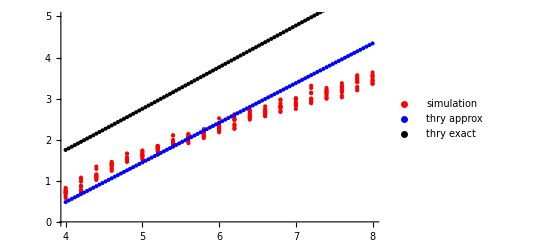

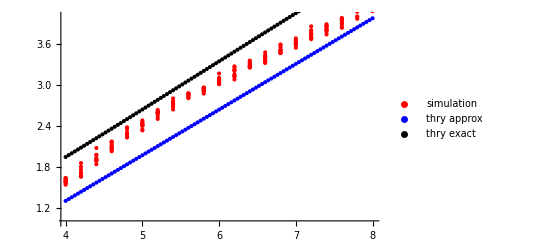

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-vary_c1-0d01_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp010.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,5}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,4}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 b *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,10^(-4-((Mod[j,21,1]-1)/10)),U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
{{(-4-((Mod[j,21,1]-1)/10)),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(-4-((Mod[j,21,1]-1)/10)),Mean[results[[;;,9]]]/Δc1}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m"];
thryvest=Table[{(-4-(i/50)),(10^5 Δc1^2(2 Log[popsize Δc1]-Log[Δc1/10^(-4-(i/50))]))/(Log[Δc1/10^(-4-(i/50))]^2)},{i,0,100}];
thryvext=Table[{(-4-(i/50)),10^5 getTransV[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
thryqest=Table[{(-4-(i/50)),-8/((-4-(i/50))+2)},{i,0,100}];
thryqext=Table[{(-4-(i/50)),getTransQ[Δc1,10^(-4-(i/50)),popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

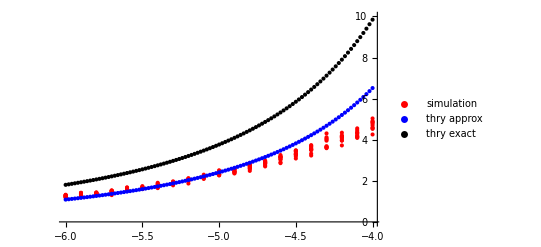

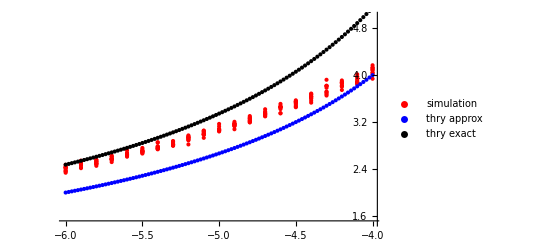

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d00_U1-vary_U2-0x10pn4_exp011.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,10}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1.5,5}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension to match Desai and Fisher simulations fig 5 & 6 c *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.00,1 10^-5,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
simv=Table[{},{i,1,210}];
simq=Table[{},{i,1,210}];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitialDFdistribution[popsize,Δc1,U1,1];
```

```mathematica
(* Run simulation *)
simdata=ParallelTable[
results=RunSimulationCheckEachMutation2[popsize,10^(-13/4+(Mod[j,21,1]-1)/10),Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
{{(-13/4+(Mod[j,21,1]-1)/10),10^5(results[[-1,4]]-results[[1,4]])/results[[-1,1]]},{(-13/4+(Mod[j,21,1]-1)/10),Mean[results[[;;,9]]]/10^(-13/4+(Mod[j,21,1]-1)/10)}}
,{j,1,210}];
simv=simdata[[;;,1]];
simq=simdata[[;;,2]];
```

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m"];
thryvest=Table[{(-13/4+(i/50)),(10^5 10^(2(-13/4+i/50))(2 Log[popsize 10^(-13/4+i/50)]-Log[10^(-13/4+i/50)/U1]))/(Log[10^(-13/4+i/50)/U1]^2)},{i,0,100}];
thryvext=Table[{(-13/4+(i/50)),10^5 getTransV[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
thryqest=Table[{(-13/4+(i/50)),(2 Log[popsize 10^(-13/4+i/50)])/Log[10^(-13/4+i/50)/U1]},{i,0,100}];
thryqext=Table[{(-13/4+(i/50)),getTransQ[10^(-13/4+i/50),U1,popsize,True]},{i,0,100}];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m",{simv,thryvest,thryvext,simq,thryqest,thryqext}];
```

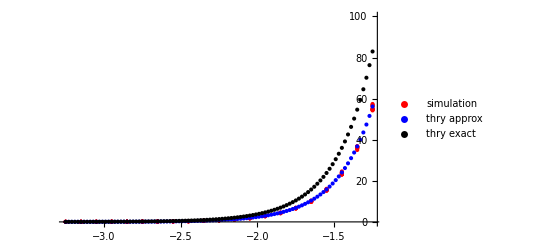

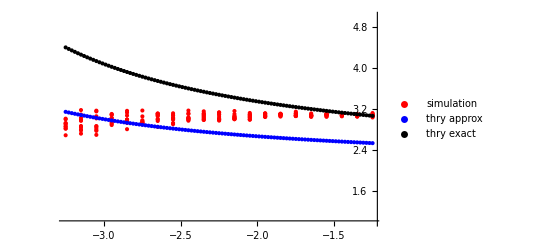

```mathematica
{simv,thryvest,thryvext,simq,thryqest,thryqext}=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-vary_c2-0d00_U1-1x10pn5_U2-0x10pn4_exp012.m"];
ListPlot[{simv,thryvest,thryvext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{0,100}]
ListPlot[{simq,thryqest,thryqext},PlotStyle->{Red,Blue,Black},PlotLegends->{"simulation","thry approx","thry exact"},Axes->True,PlotRange->{1,5}]
```

```mathematica
(* ------------------------------------------------------------------------------------------------------------ *)
(* ------------------------------------------------------------------------------------------------------------ *)
(* ------------------------------------------------------------------------------------------------------------ *)
(* Code to Test and Debug mutation modules *)

(* Set parameters for simulation of taus *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,0 10^-4,10^7};
{starttime,timestep,maxtime,globaltime}={0,(50 Log[Δc1/U1]^2)/(Δc1(2Log[popsize Δc1]-Log[Δc1/U1])),(50 Log[Δc1/U1]^2)/(Δc1(2Log[popsize Δc1]-Log[Δc1/U1])),0}; 
{verbose,veryverbose,time1,time2,time3,time4}={False,False,{0,0},{0,0},{0,0},{0,0}};
genotypes ={{1,0},{2,0}};
genotypeabundances={popsize-1/Δc1,1/Δc1};
meanFit = genotypes;
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
(* Sample the tau's to compare with theoretical distribution *)
taus = ParallelTable[
(* asdf *)
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,genotypeabundances,starttime,timestep][[1]]
(* asdf *)
,{i,1,5000}];
(* rootaddress="C:/Users/dirge/Documents/kgrel2d/"; *)
rootaddress="~/Documents/kgrel2d/";
workingfilename="_N-10p07_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp1.m";
Export[rootaddress<>"data/simtest/tauData"<>workingfilename,{taus,sol}];
rootaddress="~/Documents/kgrel2d/";
workingfilename="_N-10p07_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp1.m";
results = Import[rootaddress<>"data/simtest/tauData"<>workingfilename];
taus = results[[1]];
sol = results[[2]];
n0=((U1 ((2Δc1)/(1+2Δc1))n2[t]/.sol[[1]])/.t->#)&;
ni=NDSolveValue[{y'[t]==n0[t],y[0]==0},y,{t,0,1000}];
f[t_]:=(n0[t]Exp[-ni[t]]);
F[t_]:=1-Exp[-ni[t]];
(* Seems like my code is working fine! *)
Show[Histogram[taus,Automatic,"PDF"],Plot[f[t],{t,0,830}]]
Plot[{F[t],1},{t,0,1000}]
```

```mathematica
(* create data file for python using simulations results from set 6 experiment *)
{results,data} = {{},{}};
Do[
results = Import["C:/Users/dirge/Documents/kgrel2d/data/simtest/simtestset6/simtest_data_set2_exp"<>ToString[i]<>".m"];
data = Join[data,results];
,{i,1,93}];
Export["C:/Users/dirge/Documents/kgrel2d/data/pythondata/sumdata_exp6.dat",data];
```

```mathematica
(* create data file for python using simulations results from set 6 experiment *)
{results,NsUparam} = {{},{}};
Do[
results = Import["C:/Users/dirge/Documents/kgrel2d/data/simtest/simtestset6/computationtimes_set2_exp"<>ToString[i]<>".m"];
NsUparam = Join[NsUparam,{results[[6]]}];
,{i,1,93}];
Export["C:/Users/dirge/Documents/kgrel2d/data/pythondata/sumparam_exp6.dat",NsUparam];
```

```mathematica
collectMyData2[globaltime_,genotypes_,genotypeabundances_,Δc1_,Δc2_,stats_]:=Module[
{popsize,ibar,jbar,r1bar,r2bar,vari,varj,covij,var,timeAvgVar1,timeAvgVar2,timeAvgCov,timeAvgVar},

(* COLLECT ALL DATA: {TIMESTAMP, GENOTYPES, GENOTYPEABUNDANCES} *)
popsize = Total[genotypeabundances];
{ibar,jbar}=((1/popsize){genotypeabundances}.genotypes)[[1]];
{r1bar,r2bar}={Δc1,Δc2}*{ibar,jbar};
covij=Δc1 Δc2 Sum[(genotypes[[i]][[1]]-ibar)(genotypes[[i]][[2]]-jbar)(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
vari=Δc1^2 Sum[(genotypes[[i]][[1]]-ibar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
varj=Δc2^2 Sum[(genotypes[[i]][[2]]-jbar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
var = vari+varj+2covij;

timeAvgVar1 = stats[[4]](stats[[1]])/globaltime+vari/globaltime;
timeAvgVar2= stats[[5]](stats[[1]])/globaltime+varj/globaltime;
timeAvgCov = stats[[6]](stats[[1]])/globaltime+covij/globaltime;
timeAvgVar= stats[[7]](stats[[1]])/globaltime+var/globaltime;

{globaltime,r1bar,r2bar,timeAvgVar1,timeAvgVar2,timeAvgCov,timeAvgVar}
]
getResultStats[results_,Δc1_,Δc2_]:=Module[{popsize,ibar,jbar,r1bar,r2bar,covij,vari,varj,var,genotypes,genotypeabundances,globaltime,stats},
genotypes=results[[1]][[2]];
genotypeabundances=results[[1]][[3]];
globaltime=results[[1]][[1]];
popsize = Total[genotypeabundances];
{ibar,jbar}=((1/popsize){genotypeabundances}.genotypes)[[1]];
{r1bar,r2bar}={Δc1,Δc2}*{ibar,jbar};
covij=Δc1 Δc2 Sum[(genotypes[[i]][[1]]-ibar)(genotypes[[i]][[2]]-jbar)(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
vari=Δc1^2 Sum[(genotypes[[i]][[1]]-ibar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
varj=Δc2^2 Sum[(genotypes[[i]][[2]]-jbar)^2(genotypeabundances[[i]]/popsize),{i,1,Length[genotypes]}];
var = vari+varj+2covij;
stats = {globaltime,r1bar,r2bar,vari,varj,covij,var};

Do[
If[Mod[results[[i]][[1]],1]==0,
stats=collectMyData2[results[[i]][[1]],results[[i]][[2]],results[[i]][[3]],Δc1,Δc2,stats];]
,{i,2,Length[results]}];
{stats}
]
```

```mathematica
(* Process simulation data for python *)
ParallelDo[ 
parameters = Import["~/Documents/kgrel2d/data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"][[6]];
results=Import["~/Documents/kgrel2d/data/simtest/simtestset9/simtest_initpop_set1_exp"<>ToString[i]<>".m"];
stats = getResultStats[results,parameters[[2]],parameters[[2]]];
time3=AbsoluteTime[];
Print["Experiment "<>ToString[i]<>" required ",(time2-time1)/60," minutes to import and ", (time3-time2)/60," minutes to process."];
initpop = {stats,results[[-1]][[2]],results[[-1]][[3]]};
Export["~/Documents/kgrel2d/data/simtest/simtestset5/python_exp"<>ToString[i]<>".m",initpop];
,{i,1,33}];
```

```mathematica
parameters = Import["~/Documents/kgrel2d/data/simtest/simtestset9/computationtimes_set1_exp1.m"];
results=Import["~/Documents/kgrel2d/data/simtest/simtestset9/simtest_initpop_set1_exp1.m"];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {{19.5,3.718567180011119×10^9},{9439.11,3.718567180012451×10^9},{653.85,3.718567179974169×10^9},{11673.05081,3.718555507249799×10^9},8486,parameters}.

```mathematica
parameters
results
```

parameters

{{{2.×10^6,1.08933,1.04783,1.30947×10^-6,1.28881×10^-6,-7.67105×10^-7,1.06407×10^-6},{{948,909},{949,908},{947,910},{948,910},{949,909},{947,911},{950,908},{950,909},{949,910},{948,911},{947,912},{948,912},{950,910},{951,908},{949,912},{948,913},{949,911},{951,909},{947,913},{951,910},{950,911},{948,914},{949,913},{950,912},{951,911},{952,909},{952,910},{950,913},{952,911},{948,915},{951,912},{949,914},{952,912},{950,914},{951,913},{953,911}},{23.3504,39.6131,20.7942,1365.46,1862.32,1162.65,124.528,39240.9,51186.9,9669.48,16168.2,2.89867×10^7,221406.,24.6874,8.03451×10^6,7.11171×10^6,118323.,23042.2,18459.3,539567.,66266.,2.24655×10^6,567292.,1.03795×10^6,473799.,39325.,49464.5,222398.,91123.,6889.3,18856.3,3334.93,796.566,782.358,261.443,281.704}}}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* MULTIPLE PARAMETER SIMULATION SCRIPT - Initialize populations parameters and data processing options *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
{s,U,popsize,starttime,timestep,maxtime}={0.01,1 10^-5,5 10^7,0,1000,2000000};
{verbose,veryverbose}={False,False};
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,s,s,U,U];
{windowsaddress,ubuntuaddress}={"C:/Users/Kevin/Documents/kgrel2d/","~/Documents/kgrel2d/"};
rootaddress=ubuntuaddress;
(*first array set exp 5 and exp 7 (exp 5 cont)*)
arrys = Table[1 10^(-3+i Log10[4]/10),{i,1,10}];
arryU =Table[10^(-6+i Log10[4]/10),{i,1,10}];
arryN=Table[5 10^(6+i Log10[20]/10),{i,1,20}];
{a1,a2,a3} = {Length[arrys],Length[arryU],Length[arryN]};
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* -------------Group Data into .DAT file for Python graphs------------------------------------------------------------ *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
ParallelDo[
{myseed,time1,time2,time3,time4}={RandomInteger[{1,10000}],{0,0},{0,0},{0,0},{0,0}};
SeedRandom[myseed];
parameterCase=Which[1≤ i≤a1,1,a1+1≤ i≤a1+a2,2,a1+a2+1≤ i≤ a1+a2+a3,3];
indxadj=Which[1≤ i≤a1,0,a1+1≤ i≤a1+a2,a1,a1+a2+1≤ i≤ a1+a2+a3,a1+a2];
Print[ToString[i]]
Which[
parameterCase==1,
parameters = Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"];
parameters[[6]]={popsize,arrys[[i-indxadj]],U};
Export[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m",N[parameters,16]];,

parameterCase==2,
parameters = Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"];
parameters[[6]]={popsize,s,arryU[[i-indxadj]]};
Export[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m",N[parameters,16]];,

parameterCase==3,
parameters = Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"];
parameters[[6]]={arryN[[i-indxadj]],s,U};
Export[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m",N[parameters,16]];
]
,{i,1,a1+a2+a3}];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* MULTIPLE PARAMETER SIMULATION SCRIPT - Initialize populations parameters and data processing options *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
{s,U,popsize,starttime,timestep,maxtime}={0.01,1 10^-5,5 10^7,0,1000,2000000};
{verbose,veryverbose}={False,False};
{windowsaddress,ubuntuaddress}={"C:/Users/Kevin/Documents/kgrel2d/","~/Documents/kgrel2d/"};
rootaddress=ubuntuaddress;
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* -------------Group Data into .DAT file for Python graphs------------------------------------------------------------ *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
NsUparam={};
results = {};
Do[
NsUparam = Join[NsUparam,Import[rootaddress<>"data/simtest/simtestset9/computationtimes_set1_exp"<>ToString[i]<>".m"][[6]]];
results = Join[results,Import[rootaddress<>"data/simtest/simtestset9/simtest_initpop_set1_exp"<>ToString[i]<>".m"]];
,{i,1,40}];
Export[rootaddress<>"data/pythondata/NsUparam.dat",N[NsUparam,16]];
Export[rootaddress<>"data/pythondata/NsUparam.dat",N[results,16]];
```

{}

{}

```mathematica
results
```

{{{2.×10^6,1.08933,1.04783,1.30947×10^-6,1.28881×10^-6,-7.67105×10^-7,1.06407×10^-6},{{948,909},{949,908},{947,910},{948,910},{949,909},{947,911},{950,908},{950,909},{949,910},{948,911},{947,912},{948,912},{950,910},{951,908},{949,912},{948,913},{949,911},{951,909},{947,913},{951,910},{950,911},{948,914},{949,913},{950,912},{951,911},{952,909},{952,910},{950,913},{952,911},{948,915},{951,912},{949,914},{952,912},{950,914},{951,913},{953,911}},{23.3504,39.6131,20.7942,1365.46,1862.32,1162.65,124.528,39240.9,51186.9,9669.48,16168.2,2.89867×10^7,221406.,24.6874,8.03451×10^6,7.11171×10^6,118323.,23042.2,18459.3,539567.,66266.,2.24655×10^6,567292.,1.03795×10^6,473799.,39325.,49464.5,222398.,91123.,6889.3,18856.3,3334.93,796.566,782.358,261.443,281.704}},{{2.×10^6,1.30008,1.40116,1.52535×10^-6,1.57573×10^-6,-8.78173×10^-7,1.34474×10^-6},{{982,1059},{981,1060},{982,1060},{981,1061},{983,1059},{982,1061},{983,1061},{981,1062},{982,1062},{983,1060},{984,1058},{984,1059},{984,1061},{983,1062},{984,1060},{981,1063},{985,1061},{982,1063},{984,1062},{985,1062},{982,1064},{986,1062},{983,1063},{985,1063},{986,1061},{987,1061},{987,1062},{986,1063},{983,1064},{984,1063},{982,1065},{987,1063},{986,1064},{988,1061}},{3.33722,58.0557,764.997,83.9119,49.3347,174060.,791618.,2443.7,162843.,1323.94,3.71104,211.067,787281.,60353.4,1436.81,921.983,4.27424×10^6,27193.8,74808.2,2.55808×10^7,75284.4,1.69135×10^7,40586.1,83054.6,542145.,90675.5,8820.17,279201.,4988.44,7143.63,2379.15,5711.47,4987.45,1052.68}},{{2.×10^6,1.76704,1.60244,2.22229×10^-6,2.14027×10^-6,-1.34273×10^-6,1.67711×10^-6},{{1163,1056},{1164,1055},{1164,1056},{1163,1057},{1165,1055},{1164,1057},{1166,1054},{1165,1056},{1163,1058},{1166,1055},{1165,1057},{1164,1058},{1167,1054},{1166,1056},{1166,1057},{1163,1059},{1165,1058},{1168,1054},{1167,1055},{1167,1057},{1166,1058},{1168,1055},{1164,1059},{1167,1056},{1167,1058},{1165,1059},{1168,1057},{1166,1059},{1169,1055},{1167,1059},{1163,1060},{1168,1058},{1168,1056},{1165,1060}},{26.1317,4.66609,6658.55,5117.9,861.035,728796.,38.479,65482.2,21393.7,1130.13,8.09188×10^6,437254.,977.144,72303.6,2.48905×10^7,20999.2,4.28829×10^6,4625.65,9485.44,5.15979×10^6,5.68512×10^6,46249.9,44954.2,1673.7,356612.,23061.,7318.73,7113.92,13887.6,139.621,569.249,6107.54,432.351,1199.68}},{{2.×10^6,2.12602,2.20675,2.71329×10^-6,2.75346×10^-6,-1.65538×10^-6,2.156×10^-6},{{1219,1265},{1220,1265},{1219,1266},{1221,1264},{1218,1267},{1220,1266},{1217,1268},{1218,1268},{1221,1265},{1219,1267},{1220,1267},{1221,1266},{1222,1264},{1222,1265},{1221,1267},{1218,1269},{1217,1269},{1219,1268},{1220,1268},{1222,1266},{1221,1268},{1222,1267},{1223,1265},{1220,1269},{1221,1269},{1222,1268},{1223,1267},{1222,1269},{1223,1268},{1220,1270},{1223,1269},{1224,1267},{1222,1270},{1221,1270}},{10.1267,345.607,324.66,101.661,499.59,304293.,21.7642,10305.8,103137.,7119.6,3.1265×10^6,1.83597×10^6,244.665,560876.,9.21225×10^6,3909.27,47.6207,5487.46,3.78315×10^6,33959.1,2.00604×10^7,9.42576×10^6,10642.7,248784.,88612.8,948875.,55951.,142091.,8800.45,3901.64,15564.4,1122.66,239.099,648.188}},{{2.×10^6,2.76111,2.70971,3.31954×10^-6,3.29392×10^-6,-1.9458×10^-6,2.72186×10^-6},{{1380,1352},{1379,1353},{1378,1354},{1380,1353},{1379,1354},{1378,1355},{1381,1352},{1380,1354},{1383,1350},{1379,1355},{1378,1356},{1381,1353},{1380,1355},{1381,1354},{1379,1356},{1377,1356},{1382,1351},{1381,1355},{1380,1356},{1382,1354},{1378,1357},{1381,1356},{1382,1355},{1382,1353},{1381,1357},{1383,1354},{1380,1357},{1379,1357},{1382,1356},{1382,1357},{1381,1358},{1383,1355},{1384,1354}},{111.123,1199.13,136.069,8407.54,54682.2,35032.2,196.023,5.59414×10^6,102.571,649836.,31366.3,464.498,1.6272×10^7,5.65616×10^6,183900.,9.30035,8.08112,1.48535×10^7,598942.,1.49326×10^6,6527.6,3.0898×10^6,434553.,430.776,808337.,163426.,32494.9,5406.99,359.55,2813.16,13161.5,8458.14,841.393}},{{2.×10^6,3.3371,3.61789,4.65325×10^-6,4.79302×10^-6,-2.99359×10^-6,3.4591×10^-6},{{1452,1571},{1451,1572},{1453,1570},{1450,1573},{1451,1573},{1452,1572},{1453,1571},{1454,1570},{1450,1574},{1453,1572},{1454,1571},{1452,1573},{1451,1574},{1455,1570},{1453,1573},{1450,1575},{1451,1575},{1452,1574},{1455,1571},{1454,1572},{1456,1570},{1453,1574},{1454,1573},{1452,1575},{1450,1576},{1456,1571},{1455,1572},{1451,1576},{1452,1576},{1453,1575},{1456,1572},{1455,1573},{1457,1570},{1453,1576},{1454,1574},{1456,1573},{1452,1577},{1455,1574},{1454,1576},{1454,1575},{1457,1572},{1451,1577},{1457,1571},{1455,1576},{1456,1574},{1452,1578},{1453,1577},{1454,1577},{1456,1576}},{33.2364,53.7008,4.36214,1.55822,19833.4,12142.6,59170.9,1726.18,341.941,60651.8,265171.,518212.,470322.,14927.2,1.49045×10^6,518.153,506733.,2.72529×10^6,1.80264×10^6,94731.2,70995.3,620877.,3.082×10^6,1.42439×10^7,1888.56,379242.,158561.,92633.9,1.74627×10^7,1.7019×10^6,1.49304×10^6,355862.,2370.84,1.12634×10^6,40898.4,2711.59,114813.,100187.,883157.,10412.6,1314.46,1062.23,865.274,1869.58,2934.55,254.333,1402.82,2850.69,40.7977}},{{2.×10^6,4.48428,4.43636,6.08478×10^-6,6.06085×10^-6,-3.85538×10^-6,4.43486×10^-6},{{1697,1679},{1695,1681},{1696,1680},{1697,1680},{1695,1682},{1696,1681},{1699,1678},{1698,1679},{1696,1682},{1695,1683},{1698,1680},{1697,1681},{1699,1680},{1698,1681},{1699,1679},{1697,1682},{1696,1683},{1699,1681},{1694,1684},{1695,1684},{1700,1680},{1700,1679},{1698,1682},{1699,1682},{1700,1681},{1697,1683},{1696,1684},{1701,1681},{1698,1683},{1700,1682},{1701,1680},{1699,1683},{1697,1684},{1699,1684},{1696,1685},{1701,1682},{1702,1681},{1700,1683},{1700,1684},{1699,1685},{1702,1682},{1701,1683}},{2.35602,5.23648,6.72982,303.261,1938.79,64.1447,8.20248,27.11,123529.,14296.6,113666.,7286.92,3.6732×10^6,500368.,469.875,251281.,228779.,2.8096×10^7,4.03663,697.363,584423.,508.534,323768.,3.59974×10^6,9.11485×10^6,57454.4,71221.3,1.72338×10^6,6845.49,743770.,15710.6,174139.,10704.2,416157.,96.6399,5502.59,81409.2,21107.7,24254.6,12647.2,303.859,28.5872}},{{2.×10^6,5.75686,5.5967,7.79773×10^-6,7.718×10^-6,-4.93671×10^-6,5.64232×10^-6},{{1898,1842},{1898,1843},{1899,1842},{1902,1839},{1898,1844},{1899,1843},{1900,1843},{1900,1842},{1899,1844},{1898,1845},{1899,1845},{1903,1839},{1901,1842},{1901,1843},{1899,1846},{1900,1844},{1898,1846},{1901,1841},{1900,1845},{1899,1847},{1900,1846},{1902,1842},{1901,1844},{1900,1847},{1899,1848},{1898,1847},{1901,1845},{1901,1846},{1899,1849},{1900,1848},{1901,1847}},{5.76019,276.715,36.2366,2.67422,1197.32,5374.12,178008.,91.3672,128373.,49446.7,6.85996×10^6,16.5689,4805.47,1603.72,2.60424×10^7,78576.4,16345.9,1.26251,244095.,1.0389×10^7,826739.,137.564,9949.29,1.47673×10^6,3.66357×10^6,528.837,8497.98,4525.51,7254.56,240.349,2239.95}},{{2.×10^6,6.90714,7.46915,9.36807×10^-6,9.64741×10^-6,-5.93651×10^-6,7.14246×10^-6},{{1981,2143},{1981,2144},{1982,2143},{1983,2142},{1980,2145},{1983,2143},{1982,2144},{1981,2145},{1983,2144},{1984,2142},{1984,2143},{1980,2146},{1983,2145},{1984,2144},{1984,2145},{1982,2145},{1985,2142},{1981,2146},{1985,2144},{1983,2146},{1985,2143},{1984,2146},{1985,2145},{1982,2146},{1984,2147},{1986,2144},{1985,2146},{1983,2147},{1985,2147},{1985,2148},{1986,2145},{1984,2148}},{3.48799,148.673,551.48,19.6003,3.19927,32627.6,1612.97,377.054,1.54277×10^6,313.725,44339.9,1.33065,2.10585×10^7,1.79281×10^6,2.38252×10^7,635.094,273.903,146.646,283172.,166382.,992.922,743058.,304019.,1299.09,194576.,1450.92,1057.24,145.637,3092.65,94.1947,45.9374,196.618}},{{2.×10^6,8.95185,9.34837,0.0000117916,0.0000119884,-7.34673×10^-6,9.08663×10^-6},{{2235,2336},{2236,2335},{2235,2337},{2236,2336},{2237,2335},{2238,2334},{2237,2336},{2236,2337},{2235,2338},{2238,2335},{2237,2337},{2238,2336},{2238,2337},{2239,2334},{2236,2338},{2237,2338},{2235,2339},{2239,2335},{2239,2336},{2238,2338},{2239,2337},{2239,2338},{2240,2336},{2237,2339},{2238,2339},{2240,2337},{2240,2338},{2239,2339},{2241,2337}},{11.0472,7.83523,1671.31,1209.2,414.082,8.26943,185268.,6205.59,4664.59,6128.63,3.17902×10^6,1.02156×10^6,3.80008×10^7,35.363,8180.24,1.27828×10^6,846.158,522.29,172928.,3.5014×10^6,1.4765×10^6,1.05466×10^6,17039.6,17883.8,31978.9,7465.67,22247.3,2012.52,1047.43}},{{2.×10^6,25.5813,25.0981,0.0000455537,0.0000453117,-0.0000328386,0.0000251882},{{2557,2508},{2558,2508},{2557,2509},{2558,2509},{2559,2508},{2559,2507},{2557,2510},{2558,2510},{2560,2508},{2559,2509},{2559,2510},{2561,2508},{2558,2511},{2560,2509},{2562,2508},{2560,2510},{2561,2509},{2559,2511}},{3.25371,30877.4,426.844,3.73804×10^6,1.00911×10^6,1.04911,21731.2,4.20739×10^7,1.3045×10^6,44592.1,1.30701×10^6,432672.,28347.3,5534.08,737.806,483.275,1893.95,91.6378}},{{2.×10^6,26.027,26.875,0.0000439938,0.0000444153,-0.0000310602,0.0000262887},{{2602,2686},{2604,2684},{2603,2686},{2602,2687},{2602,2688},{2603,2687},{2604,2686},{2602,2689},{2604,2687},{2603,2688},{2605,2686},{2603,2689},{2604,2688},{2602,2690},{2605,2687},{2604,2689},{2605,2688}},{2527.86,1.36433,550472.,923640.,1.81661×10^7,1.50653×10^7,4.5037×10^6,4.73091×10^6,3.81786×10^6,1.85249×10^6,3897.24,91708.8,279413.,9891.21,2003.95,35.1445,63.6181}},{{2.×10^6,27.6432,27.2287,0.0000453994,0.0000451937,-0.000031669,0.0000272549},{{2764,2721},{2763,2722},{2762,2723},{2764,2722},{2766,2719},{2765,2721},{2763,2723},{2764,2723},{2766,2721},{2762,2724},{2765,2722},{2767,2719},{2764,2724},{2762,2725},{2765,2723},{2766,2722},{2767,2721},{2765,2724},{2762,2726},{2766,2723},{2764,2725},{2766,2724},{2768,2721},{2765,2725},{2767,2722}},{514.028,611.648,13.0439,771994.,1.09187,12099.4,671.666,3.47849×10^7,2.80167×10^6,396.019,1.50658×10^6,10.8197,1.92794×10^6,2003.11,7.73218×10^6,287839.,98872.2,69552.2,366.139,522.816,975.876,95.5367,93.5677,126.392,13.2753}},{{2.×10^6,28.0784,28.83,0.0000467788,0.000047155,-0.000032836,0.0000282618},{{2810,2878},{2811,2877},{2805,2883},{2806,2882},{2809,2879},{2807,2881},{2808,2880},{2806,2883},{2805,2884},{2810,2879},{2811,2878},{2812,2877},{2807,2882},{2807,2883},{2810,2880},{2808,2881},{2811,2879},{2805,2885},{2806,2884},{2809,2880},{2808,2883},{2812,2878},{2808,2882},{2807,2884},{2813,2877},{2811,2880},{2808,2884},{2810,2881},{2812,2880},{2806,2885},{2809,2883},{2809,2884},{2812,2881},{2808,2885},{2810,2884},{2809,2885},{2810,2883},{2811,2881},{2813,2881}},{374.668,569.278,1350.52,141.636,11.6038,10.0141,8.05683,721621.,221299.,139745.,35272.6,17161.1,6740.81,1.91975×10^7,1.92452×10^6,24.0997,198240.,454718.,228305.,1.1485,1.45574×10^7,4237.98,6519.12,63108.7,1076.43,877995.,4.67653×10^6,15306.,386852.,5431.16,815973.,5.41166×10^6,15361.1,4151.61,3522.73,3087.19,3639.8,421.334,92.9186}},{{2.×10^6,29.1221,29.687,0.0000511653,0.0000514469,-0.000036709,0.0000291942},{{2911,2968},{2912,2967},{2910,2969},{2912,2968},{2913,2966},{2911,2969},{2913,2967},{2912,2969},{2913,2968},{2910,2970},{2911,2970},{2913,2969},{2912,2970},{2914,2968},{2914,2969},{2912,2971},{2913,2970},{2914,2970}},{3026.06,65.0624,17.9405,8.00752×10^6,4.24417,33180.5,1016.93,2.90883×10^7,9.11697×10^6,15.7412,23140.1,1.17106×10^6,2.38811×10^6,130150.,16050.8,21181.2,179.71,25.357}},{{2.×10^6,30.3856,30.8331,0.0000520327,0.0000522547,-0.0000369527,0.0000303819},{{3038,3082},{3040,3080},{3037,3083},{3041,3079},{3038,3083},{3039,3081},{3039,3082},{3040,3081},{3039,3083},{3038,3084},{3037,3084},{3042,3079},{3041,3080},{3040,3083},{3038,3085},{3039,3084},{3040,3082},{3038,3086},{3039,3085},{3041,3083},{3040,3084},{3041,3084}},{27607.4,403.926,102.42,17.5002,1.1361×10^7,27.2836,36139.8,2679.97,2.37864×10^7,9.99275×10^6,899.507,1712.71,492.445,1.78449×10^6,2.43287×10^6,541382.,2585.23,19465.1,7603.17,410.957,881.812,83.8291}},{{2.×10^6,31.6981,31.7734,0.0000515798,0.0000516196,-0.0000358562,0.000031487},{{3168,3176},{3168,3177},{3169,3176},{3168,3178},{3169,3177},{3170,3176},{3170,3177},{3168,3179},{3169,3178},{3170,3178},{3171,3177},{3169,3179},{3171,3176},{3168,3180},{3171,3178},{3170,3179},{3172,3177},{3169,3180},{3171,3179},{3172,3178}},{6.08771,13320.7,2815.8,1.15439×10^6,1.44197×10^6,19832.,3.33061×10^7,3.66869×10^6,761336.,6.47558×10^6,2.29837×10^6,306169.,70.1502,72547.4,440631.,34910.1,1102.8,697.109,836.958,648.305}},{{2.×10^6,33.857,32.347,0.000049914,0.0000491649,-0.0000331237,0.0000328314},{{3383,3235},{3382,3236},{3384,3234},{3385,3234},{3383,3236},{3384,3235},{3382,3237},{3385,3235},{3386,3234},{3384,3236},{3383,3237},{3386,3233},{3386,3235},{3387,3234},{3385,3236},{3384,3237},{3382,3238},{3383,3238},{3387,3235},{3386,3236},{3388,3234},{3384,3238},{3387,3236},{3385,3237},{3388,3235}},{14.435,2.91344,5.4944,201229.,19038.,10753.1,643.697,2.21846×10^7,7.30583×10^6,66690.4,319354.,1.33304,7.75712×10^6,1.037×10^7,595705.,692067.,69.8199,32393.,420615.,15564.5,6022.65,119.614,760.523,325.111,1099.6}},{{2.×10^6,33.464,35.363,0.0000589446,0.0000598853,-0.0000423567,0.0000341166},{{3344,3536},{3345,3535},{3342,3538},{3343,3537},{3345,3536},{3344,3537},{3346,3535},{3343,3538},{3342,3539},{3346,3536},{3345,3537},{3344,3538},{3347,3535},{3347,3536},{3343,3539},{3346,3537},{3345,3538},{3344,3539},{3347,3537},{3342,3540},{3348,3535},{3348,3536},{3348,3537},{3345,3539},{3347,3538},{3349,3536},{3346,3538},{3344,3540}},{200.729,394.175,18.3255,11.5713,201950.,248100.,33596.4,1219.55,1220.9,1.99627×10^7,1.13477×10^6,1.31706×10^6,258688.,1.6915×10^7,3835.99,294261.,349610.,538129.,8.53755×10^6,59.7434,3158.26,174745.,21338.8,262.619,2072.17,91.7255,22.3825,15.8543}},{{2.×10^6,36.0611,35.0983,0.0000560863,0.0000556078,-0.0000382177,0.0000352588},{{3605,3508},{3605,3509},{3606,3508},{3605,3510},{3606,3509},{3607,3507},{3607,3508},{3606,3510},{3605,3511},{3607,3509},{3608,3509},{3605,3512},{3606,3511},{3607,3510},{3608,3508},{3609,3509},{3607,3511},{3605,3513},{3608,3510},{3606,3512}},{17.2158,54782.8,525.405,6.771×10^6,489827.,8.64585,14579.7,1.55806×10^7,6.90088×10^6,1.57601×10^7,1.83103×10^6,1.10244×10^6,568116.,921326.,102.698,281.079,1800.61,306.595,207.835,1974.1}},{{2.×10^6,39.1705,39.0796,0.0000535453,0.0000534971,-0.000034134,0.0000387743},{{3916,3906},{3917,3905},{3915,3907},{3915,3908},{3917,3906},{3916,3907},{3918,3905},{3917,3907},{3915,3909},{3918,3906},{3916,3908},{3917,3908},{3918,3907},{3919,3906},{3916,3909},{3915,3910},{3917,3909},{3918,3908},{3916,3910},{3919,3907},{3916,3911},{3918,3909},{3920,3906},{3919,3908},{3917,3910},{3915,3911}},{6.28131,22.9956,35.0534,15562.9,4887.91,300.464,34.2904,353796.,90129.2,145610.,14920.2,5.06663×10^6,241116.,36727.5,8283.37,60906.4,449762.,241458.,3972.75,1535.48,1105.7,5747.83,475.449,1637.88,1723.15,26.437}},{{2.×10^6,39.9958,40.332,0.0000567411,0.0000569099,-0.000036935,0.000039781},{{3998,4032},{3999,4032},{3998,4033},{3999,4033},{3998,4034},{4000,4032},{4001,4030},{4000,4033},{3999,4034},{3998,4035},{4001,4032},{4001,4033},{3999,4035},{4000,4034},{4001,4034},{4002,4032},{4002,4033},{4000,4035},{3999,4036},{4001,4035}},{231.519,27655.7,27418.2,1.66344×10^6,874257.,751232.,16.6522,2.70255×10^6,1.49396×10^6,4854.65,164938.,1.15351×10^6,136694.,72738.2,25238.2,468.054,1595.3,1357.74,289.491,366.642}},{{2.×10^6,40.752,41.8639,0.0000583884,0.0000589364,-0.0000382169,0.0000408909},{{4077,4181},{4078,4180},{4074,4184},{4074,4185},{4078,4181},{4077,4182},{4079,4180},{4075,4184},{4076,4183},{4074,4186},{4075,4185},{4078,4182},{4079,4181},{4075,4186},{4080,4180},{4076,4184},{4074,4187},{4075,4187},{4076,4185},{4076,4186},{4078,4183},{4077,4183},{4079,4182},{4074,4188},{4075,4188},{4076,4187},{4077,4185},{4077,4186},{4078,4185},{4075,4189},{4077,4187},{4076,4188}},{4.8184,1.12,1.36361,5537.79,339.058,37.2655,21.1392,41.4644,21.2352,460529.,17511.1,4275.28,57.0975,4.28629×10^6,73.523,83.0472,121061.,4.07754×10^6,25733.9,2.90627×10^6,823.394,1.65672,1042.48,4657.44,318769.,35440.,666.076,10164.9,2902.32,2014.73,252.599,109.563}},{{2.×10^6,42.5222,42.0302,0.0000624623,0.0000622218,-0.000041429,0.0000418261},{{4248,4204},{4250,4202},{4251,4202},{4248,4205},{4251,4203},{4249,4204},{4250,4203},{4247,4206},{4252,4202},{4252,4203},{4250,4204},{4249,4205},{4248,4206},{4251,4204},{4247,4207},{4252,4204},{4253,4202},{4253,4203},{4250,4205},{4254,4203},{4251,4205},{4253,4204},{4255,4203},{4254,4204},{4252,4205},{4253,4205}},{5.29398,1.03253,5253.17,257.789,712506.,32.3622,23.4728,14.3742,20708.,1.11505×10^7,78.7088,404.663,175.014,83313.6,238.666,180431.,7572.73,4.27005×10^6,5892.31,79223.5,1267.19,52455.6,650.707,917.587,161.779,114.229}},{{2.×10^6,43.0587,44.1611,0.0000637083,0.000064252,-0.0000424194,0.0000431215},{{4304,4415},{4305,4414},{4305,4415},{4304,4416},{4306,4414},{4306,4415},{4305,4416},{4306,4416},{4304,4417},{4305,4417},{4307,4415},{4307,4414},{4307,4416},{4306,4417},{4305,4418},{4307,4417},{4308,4415},{4306,4418},{4308,4416},{4305,4419},{4308,4417},{4307,4418}},{331.693,35.7013,223571.,1913.95,185.313,1.34107×10^6,3.8521×10^6,9.56598×10^6,1352.03,2.31613×10^6,100115.,266.833,3.04771×10^6,1.58319×10^6,5368.19,313668.,2758.25,1612.22,1097.36,2078.77,103.159,46.0576}},{{2.×10^6,45.1785,43.9116,0.000067395,0.0000667684,-0.0000450727,0.0000440179},{{4517,4389},{4516,4390},{4520,4386},{4518,4388},{4519,4387},{4518,4389},{4517,4390},{4516,4391},{4520,4387},{4518,4390},{4517,4391},{4519,4389},{4521,4386},{4519,4388},{4518,4391},{4517,4392},{4521,4387},{4520,4388},{4520,4389},{4519,4390},{4518,4392},{4519,4391},{4516,4392},{4517,4393},{4521,4388},{4521,4389},{4520,4390},{4522,4387},{4517,4394},{4518,4393},{4520,4391},{4519,4392},{4520,4392},{4518,4394},{4519,4393},{4517,4395},{4522,4389}},{388.667,13.4756,3.90066,5.26949,1.07917,107751.,82498.8,99.8631,1186.75,397274.,2.84439×10^6,68595.,54.4261,15.2814,1.63557×10^7,4.8247×10^6,9012.93,10158.2,1.46598×10^6,325964.,2.26623×10^6,427056.,59.9698,667108.,1056.22,26578.9,18025.,276.969,145154.,113334.,4473.21,6331.15,451.272,579.148,215.086,122.933,36.0824}},{{2.×10^6,45.4088,45.4109,0.0000680517,0.0000680553,-0.000045625,0.000044857},{{4538,4540},{4538,4541},{4539,4540},{4539,4541},{4540,4539},{4538,4542},{4540,4540},{4541,4539},{4540,4541},{4539,4542},{4541,4540},{4541,4541},{4538,4543},{4540,4542},{4542,4539},{4539,4543},{4542,4541},{4541,4542},{4540,4543},{4542,4542},{4539,4544},{4543,4541},{4542,4540},{4541,4543}},{9.3004,10711.6,2173.72,1.51988×10^6,26.5397,48917.9,91542.1,7576.14,3.23295×10^6,1.88827×10^6,6768.35,2.49091×10^7,9287.49,1.44098×10^6,5447.43,126205.,7.0818×10^6,312221.,12007.3,1532.92,49.2969,677.625,75.8009,805.851}},{{2.×10^6,46.7126,46.2002,0.0000688897,0.0000686367,-0.0000458315,0.0000458634},{{4669,4619},{4670,4618},{4668,4620},{4670,4619},{4671,4618},{4669,4620},{4668,4621},{4671,4619},{4672,4618},{4670,4620},{4675,4614},{4669,4621},{4671,4620},{4668,4622},{4672,4619},{4670,4621},{4673,4618},{4672,4620},{4671,4621},{4670,4622},{4669,4622},{4673,4619},{4672,4621},{4673,4620},{4670,4623},{4671,4622},{4673,4621},{4674,4620},{4672,4622}},{125.181,16.5374,11.2657,47398.8,13729.9,1413.71,1301.79,6.90679×10^6,66439.7,3636.06,3.21637,41628.1,2.15906×10^7,981.19,2.93941×10^6,1.6253×10^6,2820.3,1.60427×10^7,402923.,4.20528×10^6,273.691,4737.66,632382.,366563.,8301.85,10256.8,10387.2,172.23,2367.32}},{{2.×10^6,47.8905,47.2859,0.0000727925,0.0000724916,-0.0000491701,0.0000469439},{{4790,4724},{4789,4725},{4787,4727},{4788,4726},{4789,4726},{4790,4725},{4787,4728},{4791,4724},{4786,4729},{4788,4727},{4789,4727},{4790,4726},{4791,4725},{4789,4728},{4788,4728},{4790,4727},{4787,4729},{4786,4730},{4791,4726},{4789,4729},{4790,4728},{4792,4724},{4792,4725},{4791,4727},{4790,4729},{4789,4730},{4788,4729},{4792,4727},{4791,4728},{4792,4726},{4789,4731},{4791,4729},{4790,4730},{4792,4728}},{11.7964,47.0748,6.33737,2.00791,28769.5,26632.3,568.66,156.341,167.66,25.4599,2.23378×10^6,74819.7,77571.4,2.07858×10^7,1151.69,1.02938×10^6,224.837,130.298,36625.8,4.76263×10^7,945763.,89.5625,968.06,601994.,416291.,193308.,358.554,23019.3,6865.87,93.2214,618.661,1408.84,398.611,132.095}},{{2.×10^6,48.9594,48.7725,0.0000767552,0.0000766632,-0.000052619,0.0000481804},{{4894,4875},{4893,4876},{4896,4873},{4895,4875},{4894,4876},{4897,4873},{4896,4874},{4893,4877},{4894,4877},{4895,4876},{4896,4875},{4897,4874},{4895,4877},{4893,4878},{4894,4878},{4898,4874},{4898,4873},{4895,4878},{4896,4877},{4896,4876},{4897,4875},{4897,4877},{4894,4879},{4895,4879},{4896,4878},{4898,4877},{4893,4879},{4898,4875},{4899,4874},{4897,4878},{4897,4876},{4898,4878},{4896,4879},{4899,4877},{4895,4880},{4898,4879},{4899,4878}},{9.60636,1.71999,2.73739,3629.77,1737.84,25.3577,398.92,196.348,268055.,13200.,47920.9,39373.8,1.25063×10^7,676.133,311181.,73470.3,7.2444,2.38665×10^7,3.89274×10^7,5960.38,2921.29,1.3745×10^7,19533.7,423629.,617803.,8.93146×10^6,69.9851,544.108,1314.12,73557.,232.17,98433.,6404.35,9592.78,2690.32,322.435,394.976}},{{2.×10^6,50.6386,49.7421,0.0000736659,0.0000732201,-0.0000487109,0.0000494642},{{5061,4973},{5062,4972},{5062,4973},{5063,4972},{5061,4974},{5060,4975},{5063,4973},{5062,4974},{5064,4972},{5063,4974},{5064,4973},{5062,4975},{5061,4975},{5060,4976},{5064,4974},{5063,4975},{5065,4973},{5064,4975},{5062,4976},{5065,4974},{5063,4976},{5064,4976},{5065,4975},{5065,4972},{5066,4973},{5063,4977},{5066,4974},{5062,4977},{5065,4976},{5067,4973}},{9.31199,17.1486,71536.8,707.698,209.409,25.5737,1.8311×10^6,2.13488×10^6,2362.74,1.5281×10^6,2.10028×10^6,613046.,52.8938,61.4812,1.03888×10^8,2.18513×10^6,65227.6,9.26127×10^6,45949.2,1.35479×10^6,9.67651×10^6,103863.,47427.6,70.9684,13036.3,1749.09,1954.51,31.3888,489.119,2.08878}},{{2.×10^6,50.2644,51.3822,0.0000772104,0.0000777598,-0.0000524594,0.0000500515},{{5027,5134},{5026,5135},{5028,5133},{5029,5132},{5028,5134},{5027,5135},{5026,5136},{5029,5133},{5030,5132},{5026,5137},{5028,5135},{5029,5134},{5027,5136},{5026,5138},{5030,5133},{5027,5137},{5029,5135},{5028,5136},{5027,5138},{5026,5139},{5030,5134},{5028,5137},{5027,5139},{5028,5138},{5026,5140},{5029,5136},{5031,5134},{5030,5135},{5028,5139},{5027,5140},{5026,5141},{5028,5140},{5029,5137},{5029,5138},{5027,5141},{5029,5139}},{84.6835,130.973,17.206,7.92803,11608.3,9008.77,2169.65,625.442,3.31844,1.31247×10^6,654102.,83758.8,12221.,7.62841×10^7,371.2,4.1608×10^6,481238.,260126.,5.01198×10^7,2.71702×10^7,30946.8,114117.,1.89038×10^7,345178.,598448.,13983.,4411.56,3858.93,120059.,1.34796×10^6,2914.41,5241.53,1565.88,501.586,523.273,48.622}},{{2.×10^6,51.0715,53.1399,0.0000777217,0.0000787433,-0.0000525915,0.0000512819},{{5106,5311},{5105,5312},{5107,5310},{5108,5309},{5106,5312},{5107,5311},{5105,5313},{5109,5309},{5108,5310},{5108,5311},{5107,5312},{5106,5313},{5105,5314},{5109,5310},{5106,5314},{5109,5311},{5108,5312},{5107,5313},{5107,5314},{5105,5315},{5108,5313},{5106,5315},{5110,5309},{5109,5312},{5107,5315},{5108,5314},{5110,5311},{5110,5310},{5109,5313},{5108,5315},{5105,5316},{5106,5316},{5107,5316},{5109,5314},{5110,5312},{5109,5315},{5110,5313},{5108,5316}},{146.944,124.148,5.96074,7.39963,18557.8,20645.4,5948.98,69.4578,128.822,1.77513×10^6,218030.,204091.,47158.8,784.11,1.36192×10^7,363966.,277650.,3.52988×10^6,1.62964×10^8,50127.4,3.4845×10^6,1.59915×10^6,24.7613,149667.,1.0808×10^7,4.53587×10^7,33183.5,20.107,133135.,882906.,2346.93,1887.6,5641.46,77535.2,1461.47,10485.3,644.366,473.434}},{{2.×10^6,52.4678,53.7096,0.0000800761,0.0000806832,-0.0000542734,0.0000522125},{{5245,5369},{5246,5368},{5245,5370},{5247,5368},{5246,5369},{5246,5370},{5247,5369},{5245,5371},{5248,5367},{5248,5368},{5246,5371},{5247,5370},{5249,5368},{5248,5369},{5245,5372},{5247,5371},{5246,5372},{5248,5370},{5249,5369},{5250,5368},{5247,5372},{5246,5373},{5245,5373},{5248,5371},{5251,5368},{5249,5370},{5247,5373},{5246,5374},{5252,5368},{5248,5372},{5250,5369},{5249,5371},{5245,5374},{5251,5369},{5247,5374},{5250,5370},{5246,5375},{5253,5368}},{131.898,260.176,273758.,21581.9,3789.96,1.47459×10^7,74328.7,634204.,1.89809,261771.,4.70824×10^7,1.8753×10^7,7.29669×10^6,1.10384×10^6,1.26047×10^6,1.67849×10^8,4.31884×10^7,9.46518×10^6,39353.8,755451.,2.93156×10^6,9.90777×10^6,80565.3,679889.,3.96905×10^6,459266.,175021.,361582.,59986.2,2606.79,3373.54,550.802,488.049,1619.37,2130.53,198.211,34.4833,356.67}},{{2.×10^6,53.3547,54.3787,0.0000806802,0.0000811844,-0.0000544595,0.0000529456},{{5335,5435},{5336,5434},{5337,5433},{5336,5435},{5335,5436},{5338,5433},{5337,5434},{5335,5437},{5336,5436},{5337,5435},{5338,5434},{5335,5438},{5337,5436},{5338,5435},{5336,5437},{5339,5433},{5339,5434},{5336,5438},{5335,5439},{5338,5436},{5339,5435},{5337,5437},{5337,5438},{5336,5439},{5340,5434},{5335,5440},{5339,5436},{5338,5437},{5338,5438},{5337,5439},{5336,5440},{5340,5435},{5339,5437},{5340,5436}},{847.958,3.23958,16.4044,38252.5,236959.,313.573,615.655,7.0041×10^6,249674.,454486.,68229.7,2.62477×10^8,895273.,1.47699×10^7,3.67707×10^6,139.347,385366.,1.45515×10^8,6.17546×10^6,1.96381×10^6,228636.,649791.,1.54849×10^6,747310.,10621.7,35156.1,50491.8,16632.1,9854.3,2702.56,1576.49,222.391,16.4406,99.1491}},{{2.×10^6,54.6475,56.2784,0.0000773621,0.000078161,-0.0000505181,0.0000544869},{{5461,5627},{5460,5628},{5462,5627},{5461,5628},{5463,5627},{5460,5629},{5462,5628},{5459,5630},{5461,5629},{5464,5627},{5463,5628},{5462,5629},{5464,5628},{5465,5627},{5462,5630},{5461,5630},{5460,5630},{5465,5628},{5463,5629},{5466,5627},{5464,5629},{5463,5630},{5465,5629},{5462,5631},{5466,5628},{5467,5627},{5464,5630},{5465,5630},{5463,5631},{5466,5629},{5467,5628},{5468,5627},{5465,5631},{5466,5630},{5468,5628},{5464,5631},{5462,5632},{5467,5629}},{448.648,2.15414,101743.,4957.82,4.40472×10^6,4.36829,192034.,9.50886,15728.2,1.63173×10^7,2.08765×10^6,1.66274×10^6,8.76247×10^7,1.31296×10^8,8.51568×10^6,9944.96,10.1928,2.55969×10^8,1.65378×10^6,3.1449×10^7,2.36123×10^7,3.34825×10^6,3.00123×10^7,50520.9,123454.,1.08793×10^6,159011.,3.39198×10^6,9740.73,63603.7,201154.,44455.3,6150.89,11.53,212.626,35.7893,814.242,52.3858}},{{2.×10^6,56.6375,55.434,0.0000901571,0.0000895605,-0.0000623612,0.0000549952},{{5660,5542},{5660,5543},{5662,5541},{5661,5542},{5660,5544},{5661,5543},{5663,5541},{5662,5542},{5661,5544},{5660,5545},{5663,5542},{5664,5541},{5662,5543},{5661,5545},{5664,5542},{5662,5544},{5663,5543},{5660,5546},{5665,5541},{5664,5543},{5662,5545},{5661,5546},{5663,5544},{5666,5541},{5665,5542},{5665,5543},{5664,5544},{5663,5545},{5661,5547},{5665,5544},{5660,5547},{5664,5545},{5662,5546},{5666,5543},{5666,5542},{5667,5541},{5667,5543},{5665,5545},{5664,5546},{5666,5544},{5662,5547},{5663,5546},{5661,5548},{5667,5544},{5668,5543},{5666,5545},{5667,5542}},{1.25727,2090.5,270.079,313.914,367319.,22103.9,20312.5,6809.22,3.08253×10^7,4.38604×10^6,4.20449×10^6,1.12659×10^6,8371.87,2.22547×10^7,4.29941×10^6,6.87261×10^6,1.42121×10^7,412911.,455855.,4.63729×10^8,2.11117×10^7,1.65081×10^7,5.95435×10^6,1.59127×10^6,1.95567×10^6,7.67264×10^7,8.8786×10^7,1.72741×10^6,899499.,2.48343×10^7,3326.85,1.62198×10^7,780015.,3.53053×10^6,36792.5,4500.53,235405.,33521.5,17665.6,13328.5,2372.96,1360.5,51.8518,86.8137,448.899,84.7355,174.159}},{{2.×10^6,56.288,57.8824,0.0000821713,0.0000829507,-0.0000545617,0.0000559985},{{5627,5785},{5627,5786},{5628,5785},{5629,5784},{5626,5787},{5627,5787},{5629,5785},{5628,5786},{5628,5787},{5630,5784},{5630,5785},{5629,5786},{5627,5788},{5625,5789},{5628,5788},{5626,5788},{5629,5787},{5627,5789},{5631,5785},{5630,5786},{5631,5784},{5628,5789},{5630,5787},{5626,5789},{5625,5790},{5629,5788},{5631,5786},{5627,5790},{5632,5785},{5629,5789},{5628,5790},{5631,5787},{5630,5788},{5632,5786},{5627,5791},{5629,5790},{5632,5784},{5632,5787},{5630,5789},{5631,5788},{5633,5785},{5629,5791},{5628,5791},{5633,5786},{5627,5792},{5630,5790},{5631,5789},{5632,5788},{5633,5787}},{4.57962,2386.83,1557.74,110.693,10.9335,23416.2,347429.,149651.,4.61763×10^7,296.082,2.66082×10^6,1.27221×10^6,1.19087×10^7,80.7758,1.76625×10^8,47.8132,9.41525×10^7,8.33289×10^6,2.11547×10^7,1.55231×10^6,1417.92,1.56553×10^8,1.02442×10^8,16.4953,90.006,1.59057×10^6,6.83124×10^6,2.27573×10^6,356816.,4.18505×10^8,1.11767×10^7,2.07673×10^7,4.6191×10^6,973456.,186180.,6.17716×10^6,294.975,276483.,1.21555×10^6,113880.,5591.35,114451.,2321.62,3884.69,5674.09,5247.1,130.882,1153.,133.116}},{{2.×10^6,59.072,57.1982,0.0000920787,0.0000911634,-0.0000631339,0.0000569744},{{5906,5717},{5907,5716},{5908,5715},{5907,5717},{5909,5715},{5906,5718},{5908,5716},{5906,5719},{5910,5715},{5907,5718},{5905,5719},{5909,5716},{5908,5717},{5906,5720},{5907,5719},{5910,5716},{5908,5718},{5911,5715},{5909,5717},{5907,5720},{5905,5720},{5908,5719},{5906,5721},{5912,5715},{5910,5717},{5911,5716},{5909,5718},{5908,5720},{5907,5721},{5909,5719},{5905,5721},{5911,5717},{5912,5716},{5910,5718},{5906,5722},{5909,5720},{5908,5721},{5910,5719},{5911,5718},{5913,5715},{5907,5722},{5912,5717},{5908,5722},{5910,5720},{5913,5716},{5909,5721},{5906,5723},{5911,5719}},{102.241,1.0776,2.1158,3996.71,11394.7,56370.4,29.6692,1.09201×10^7,1.34052×10^6,2.64571×10^6,5.24156,145260.,326911.,6.80208×10^7,9.77914×10^6,2.09245×10^7,1.56594×10^7,4.47514×10^6,851336.,1.12694×10^9,283.002,1.96254×10^7,1.87648×10^7,424667.,4.31124×10^6,4.04982×10^6,1.10451×10^6,1.04681×10^8,4.68912×10^6,4.85216×10^7,587.378,404540.,629897.,5.87296×10^6,333469.,4.94432×10^6,1.51611×10^6,169583.,75600.4,1622.74,3326.73,16546.2,6361.33,13513.2,2191.42,4344.79,69.2895,509.391}},{{2.×10^6,59.7211,59.1773,0.0000851171,0.0000848531,-0.0000558688,0.0000582326},{{5970,5915},{5970,5916},{5969,5917},{5971,5915},{5972,5914},{5971,5916},{5972,5915},{5970,5917},{5969,5918},{5972,5916},{5971,5917},{5973,5915},{5970,5918},{5972,5917},{5973,5916},{5969,5919},{5973,5914},{5972,5918},{5971,5918},{5973,5917},{5974,5915},{5974,5916},{5970,5919},{5973,5918},{5972,5919},{5969,5920},{5975,5915},{5974,5917},{5975,5916},{5971,5919},{5973,5919},{5974,5918},{5975,5917},{5972,5920},{5970,5920},{5976,5915},{5974,5919},{5973,5920},{5976,5916},{5975,5918},{5976,5917}},{5.81019,2845.79,302.431,4198.62,1.55174,500952.,126520.,2301.74,11413.9,8.35215×10^6,2.01135×10^6,255908.,60624.1,3.07595×10^8,2.17413×10^7,5827.92,1.2272,1.45012×10^9,278558.,1.69806×10^8,165924.,4.07984×10^6,2642.79,2.2765×10^7,6.97532×10^6,11471.6,40663.6,931702.,26982.2,1541.77,3.27833×10^6,615826.,215621.,5273.32,231.943,1202.57,1242.35,1127.73,67.295,6600.77,39.3933}}}